# Coupled square well scattering and bound states

## A “simple” multichannel model

## 1-channel square well

As a preliminary to the multichannel case, we will need to solve the single channel case to understand where the bound states are with respect to the threshold.  This will help us interpret the two-channel resonances, at least in the weak coupling regime.  Inside the well of range r_0, the radial wavefunction R(r) satisfies:

(-ℏ^2/(2μ)1/r^2∂/(∂r)r^2∂/(∂r)+(-V_0-E)+(L(L+1))/r^2) R(r)=0

We let ψ(r)=r R(r)

(-ℏ^2/(2μ)∂^2/(∂r^2)+(-V_0-E)+(L(L+1))/r^2)ψ(r)=0

(∂^2/(∂r^2)+(2μ)/ℏ^2(E+V_0)-(L(L+1))/r^2) ψ(r)=0

Let ϵ=(2μ r_0^2 E)/ℏ^2 and v_0=(2μ r_0^2 V_0)/ℏ^2.  Also RESCALE r→r/r_0.  Then

(∂^2/(∂r^2)+ϵ+v_0-(L(L+1))/r^2)ψ(r)=0

When v_0=0, with x=√ϵ r the solutions are:

```mathematica
DSolve[ψ''[x]+1ψ[x]-(L(L+1))/x^2 ψ[x]==0,ψ,x]
```

{{ψ→Function[{x},√x BesselJ[1/2 (1+2 L),x] C[1]+√x BesselY[1/2 (1+2 L),x] C[2]]}}

(∂^2/(∂x^2)+1-(L(L+1))/x^2)ψ=0

ψ(x) ~ √x[A_L J_(L+1/2)(x)+B_L Y_(L+1/2)(x)]

The fundamental unit of length is r_0, the unit of energy is ℏ^2/(2μ r_0^2).

Then inside,

ψ_in(r)= √(π/2 √(ϵ+v_0)r) J_(L+1/2)(√(ϵ+v_0)r)

```mathematica
ψIn[L_,x_]=√(π/2 x)BesselJ[L+1/2,x]
```

√(π/2) √x BesselJ[1/2+L,x]

Where it is assumed that x=k_in r=√(ϵ+v_0)r.

Outside (for bound states ϵ<0),

ψ_Bout(r)=√(π/2 √-ϵ r)K_L(√-ϵ r)

```mathematica
ψBOut[L_,x_]:=√(π/2 x)BesselK[L+1/2,x]
```

while for scattering states with ϵ>0:

ψ_Sout(r)=√(π/2 √ϵ r)(cos δ_L J_(L+1/2)(√ϵ r)- sin δ_L Y_(L+1/2)(√ϵ r)) ~ √(√ϵ r)(J_(L+1/2)(√ϵ r)- tan δ_L Y_(L+1/2)(√ϵ r))

Where tan δ_L=K_L, the K-matrix element.

```mathematica
ψSOut[L_,x_]:=√x(BesselJ[L+1/2,x]-KL BesselY[L+1/2,x])
```

Let’s focus on the bound states.  Matching the log-derivatives gives:

```mathematica
TEQ0=FullSimplify[D[Log[ψIn[L,√(ϵ+v0) r]],r]-D[Log[ψBOut[L,√-ϵ r]],r]/.{L->0,r->1}]
```

√-ϵ+√(v0+ϵ) Cot[√(v0+ϵ)]

Let’s make this easier to handle by multiplying through by sin(√(ϵ+v_0)) (it’s all equal to zero anyhow, so this doesn’t change the position of the roots.)

For s-waves:

```mathematica
TEQ0=FullSimplify[Sin[√(ϵ+v0)](D[Log[ψIn[L,√(ϵ+v0) r]],r]-D[Log[ψBOut[L,√-ϵ r]],r])/.{L->0,r->1}]
```

√(v0+ϵ) Cos[√(v0+ϵ)]+√-ϵ Sin[√(v0+ϵ)]

for p-waves:

```mathematica
TEQ1=FullSimplify[FunctionExpand[((1+√-ϵ) ((v0+ϵ) Cos[√(v0+ϵ)]-√(v0+ϵ) Sin[√(v0+ϵ)]))(D[Log[ψIn[L,√(ϵ+v0) r]],r]-D[Log[ψBOut[L,√-ϵ r]],r])/.{L->1,r->1}]]
```

-ϵ (v0+ϵ) Cos[√(v0+ϵ)]-√(v0+ϵ) (v0+v0 √-ϵ+√-ϵ ϵ) Sin[√(v0+ϵ)]

For d-waves,

```mathematica
TEQ2=FullSimplify[FunctionExpand[(-3 √-ϵ+(3+√-ϵ) ϵ) (3 √(v0+ϵ) Cos[√(v0+ϵ)]+(-3+v0+ϵ) Sin[√(v0+ϵ)])(D[Log[ψIn[L,√(ϵ+v0) r]],r]-D[Log[ψBOut[L,√-ϵ r]],r])/.{L->2,r->1}]]
```

√(v0+ϵ) ((-ϵ)^(5/2)+v0 (-3 √-ϵ+(3+√-ϵ) ϵ)) Cos[√(v0+ϵ)]+(3 v0 √-ϵ-ϵ^3-v0 ϵ (3+ϵ)) Sin[√(v0+ϵ)]

For purposes of root-finding, we’ll need to make a guess as to where the roots are.  Since we know the solutions in the interior region are simply Bessel functions, we can find approximate positions of the roots by treating the finite well like an infinite well and using the known zeroes of the Bessel function.  The additional “fudge factor” of (π/4 n)^2 seems to work well in correcting the high-lying states.

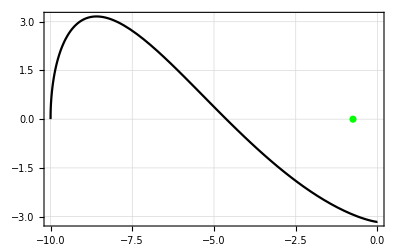

```mathematica
Vmax=10;
rootguess0=Table[{-Vmax +N[BesselJZero[1/2,n]]^2-(π/4 n)^2,0},{n,1,20}];
p2=ListPlot[rootguess0,PlotStyle->Green];
p3=Plot[TEQ0/.v0->Vmax,{ϵ,-Vmax,0},PlotStyle->Black];Show[{p2,p3},PlotRange->{{-Vmax,0},All},Frame->True,GridLines->Automatic]
```

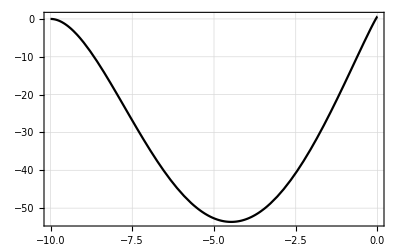

```mathematica
Vmax=10;
rootguess1=Table[{-Vmax+N[BesselJZero[3/2,n]]^2-(2.4 n)^2,0},{n,1,20}];
p2=ListPlot[rootguess1,PlotStyle->Green];
p3=Plot[TEQ1/.v0->Vmax,{ϵ,-Vmax,0},PlotStyle->Black];Show[{p2,p3},PlotRange->{{-Vmax,0},All},Frame->True,GridLines->Automatic]
```

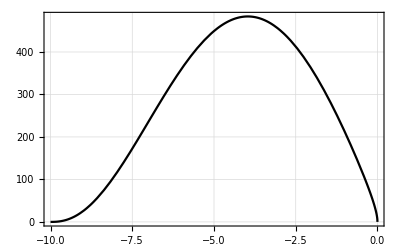

```mathematica
Vmax=10;
rootguess2=Table[{-Vmax+N[BesselJZero[5/2,n]]^2-(π/4 n)^2,0},{n,1,20}];
p2=ListPlot[rootguess2,PlotStyle->Green];
p3=Plot[TEQ2/.v0->Vmax,{ϵ,-Vmax,0},PlotStyle->Black];Show[{p2,p3},PlotRange->{{-Vmax,0},All},Frame->True,GridLines->Automatic]
```

```mathematica
rootguess0=Select[Table[{-Vmax+N[BesselJZero[1/2,n]]^2-(π/4 n)^2,0},{n,1,50}],#[[1]]<100&]
```

{{-0.747246,0},{27.011,0},{73.2748,0}}

It’s also very helpful to know when there is a state at threshold.  So for what V_0 is the energy zero?

```mathematica
V0roots0=Sort[DeleteDuplicates[Table[v0/.FindRoot[TEQ0/.ϵ->0,{v0,vn}],{vn,2,Vmax,1}],(Abs[#1-#2]<10^-4&)]]
```

{9.13194×10^-22+0. ⅈ,2.4674}

```mathematica
V0roots0Table=Table[{V0roots0[[n]],0},{n,1,Length[V0roots0]}]
```

{{9.13194×10^-22+0. ⅈ,0},{2.4674,0}}

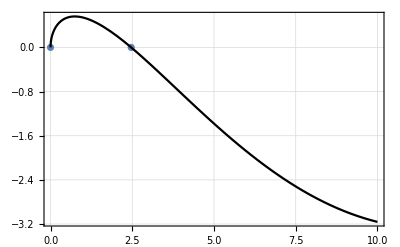

```mathematica
pv0=ListPlot[V0roots0Table];p0=Plot[TEQ0/.{ϵ->0},{v0,0,Vmax},PlotStyle->Black];Show[{pv0,p0},PlotRange->{{0,Vmax},All},Frame->True,GridLines->Automatic]
```

```mathematica
V0roots0[[2]]
```

2.4674

```mathematica
ϵ/.FindRoot[TEQ0/.v0->Vmax,{ϵ,-Vmax+N[BesselJZero[1/2,n]]^2-(π/4 n)^2}]/.n->1
```

-4.62419

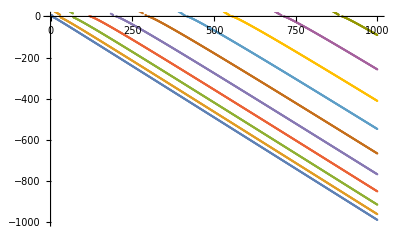

```mathematica
Vmax=1000;ListPlot[Table[{VV,ϵ/.FindRoot[TEQ0/.v0->VV,{ϵ,-VV+N[BesselJZero[1/2,n]]^2-(π/4 n)^2}]},{n,1,10},{VV,2.5,Vmax}],PlotRange->{{0,Vmax},{-Vmax,0}}]
```

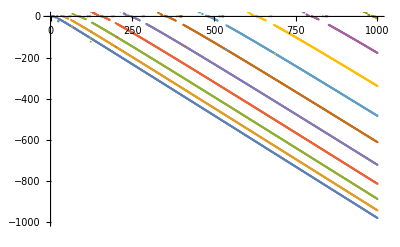

```mathematica
Vmax=1000;ListPlot[Table[{VV,ϵ/.FindRoot[TEQ1/.v0->VV,{ϵ,-VV+N[BesselJZero[3/2,n]]^2-(π/4 n)^2}]},{n,1,10},{VV,3,Vmax}],PlotRange->{{0,Vmax},{-Vmax,0}}]
```

Okay, there are some numerical quirks that need to be worked out here, and the code is clunky to be sure, but more or less this is right.

## 2-channel model

Let’s work through the two-channel physics before trying N channels.  In the interior region,

(-ℏ^2/(2μ)∂^2/(∂r^2)+V_1(r)+(ℏ^2 L(L+1))/(2μ r^2) | V_12
V_12 | -ℏ^2/(2μ)∂^2/(∂r^2)+V_2(r)+(ℏ^2 L(L+1))/(2μ r^2))( ψ_1
 ψ_2)=E (ψ_1
ψ_2)

Choose:

V_1(r)={-V_1
0         for  r<r_0
for r>r_0

V_2(r)={E_2^th-V_2
E_2^th      for  r<r_0
for r>r_0

We wish to measure length in units of r_0, and energy in units of ℏ^2/(2μ r_0^2), so we multiply through by r_0^2, and redefine r→ r/r_0:

(∂^2/(∂r^2)+(2μ r_0^2)/ℏ^2(V_1+E)-(L(L+1))/r^2 | (2μ r_0^2)/ℏ^2 V_12
(2μ r_0^2)/ℏ^2 V_12* | ∂^2/(∂r^2)+(2μ r_0^2)/ℏ^2(V_2-E_2^th+E)-(L(L+1))/r^2)(ψ_1^I
ψ_2^I)=0

Now note that for the scattering problem E>0.  By definition, V_i>0 ∀i and also, E_i^th>0 ∀i.

Let’s define

g_ij=(2μ r_0^2)/ℏ^2 V_ij  is a dimensionless coupling,

v_i= γ_i^2=(2μ r_0^2)/ℏ^2 V_i>0  is a wavenumber (squared) that measures the depth of the well in channel i,

ϵ=k^2=(2μ r_0^2)/ℏ^2 E  is the wavenumber in the asymptotic region of the open channel,

ϵ_i=β_i^2=(2μ r_0^2)/ℏ^2 E_i^th>0  is a wavenumber (squared) measuring the threshold energy of channel i.

(∂^2/(∂r^2)+(ϵ+v_1)-(L(L+1))/ρ^2 | g
g | ∂^2/(∂r^2)+(ϵ+v_2-ϵ_2)-(L(L+1))/r^2)(ψ_1^I
ψ_2^I)=0

Write this as:

(∂^2/(∂r^2)+(ϵ+v_1)-(L(L+1))/ρ^2 | g
g | ∂^2/(∂r^2)+(ϵ+v_2-ϵ_2)-(L(L+1))/r^2)(ψ_1^I
ψ_2^I)=0

[(∂^2/(∂r^2)-(L(L+1))/r^2 | 0
0 | ∂^2/(∂r^2)-(L(L+1))/r^2)+((ϵ+v_1) | g
g | (ϵ+v_2-ϵ_2))](ψ_1^I
 ψ_2^I)=0

In the exterior region (II),  r>r_0=1, we have:

[(∂^2/(∂r^2)-(L(L+1))/r^2 | 0
0 | ∂^2/(∂r^2)-(L(L+1))/r^2)+(ϵ | 0
0 | ϵ-ϵ_i)](ψ_1^II
ψ_2^II)=0

### “Dressed state” or “adiabatic” picture

In the interior region, the situation is more complicated due to the coupling.  It turns out that it is still possible to solve the problem exactly.  The trick is to use “dressed” states that are eigenstates of the constant matrix (assume g is real):

W=((ϵ+v_1) | g
g | (ϵ+v_2-ϵ_2))

```mathematica
Clear[g,ϵ,v1,v2]
```

```mathematica
W=({{(ϵ+v1), g}, {g, (ϵ+v2-ϵ2)}})
```

{{v1+ϵ,g},{g,v2+ϵ-ϵ2}}

```mathematica
Avecs=FullSimplify[Eigenvectors[W],Assumptions->{k∈Reals,Subscript[γ, 1]∈Reals,Subscript[γ, 2]∈Reals,Subscript[ν, 2]∈Reals,g∈Reals}]
```

{{(v1-v2+ϵ2-√(4 g^2+(v1-v2+ϵ2)^2))/(2 g),1},{(v1-v2+ϵ2+√(4 g^2+(v1-v2+ϵ2)^2))/(2 g),1}}

Define an orthogonal matrix comprised of normalized eigenvectors in the columns of the matrix.  Mathematica puts eigenvectors in the rows, so I’ll define this as the transpose of the output of “Eigenvectors” above:

```mathematica
AvecsNormed=Transpose[Table[FullSimplify[Normalize[Avecs[[n]]],Assumptions->{ϵ∈Reals,v1>0,v2>0,ϵ2>0,g∈Reals}],{n,1,2}]]
```

{{(v1-v2+ϵ2-√(4 g^2+(v1-v2+ϵ2)^2))/(g √(4+((v1-v2+ϵ2-√(4 g^2+(v1-v2+ϵ2)^2))^2)/g^2)),(v1-v2+ϵ2+√(4 g^2+(v1-v2+ϵ2)^2))/(g √(4+((v1-v2+ϵ2+√(4 g^2+(v1-v2+ϵ2)^2))^2)/g^2))},{2/(√(4+((v1-v2+ϵ2-√(4 g^2+(v1-v2+ϵ2)^2))^2)/g^2)),2/(√(4+((v1-v2+ϵ2+√(4 g^2+(v1-v2+ϵ2)^2))^2)/g^2))}}

```mathematica
Avals=Simplify[Eigenvalues[W],Assumptions->{ϵ∈Reals,v1>0,v2>0,ϵ2>0,g∈Reals}]
```

{1/2 (v1+v2+2 ϵ-ϵ2-√(4 g^2+(v1-v2+ϵ2)^2)),1/2 (v1+v2+2 ϵ-ϵ2+√(4 g^2+(v1-v2+ϵ2)^2))}

Let’s check that the matrix of eigenvectors is properly normalized:

```mathematica
MatrixForm[FullSimplify[AvecsNormed.AvecsNormedᵀ]]
```

(1 | 0
0 | 1)

```mathematica
MatrixForm[FullSimplify[AvecsNormedᵀ.AvecsNormed]]
```

(1 | 0
0 | 1)

```mathematica
MatrixForm[FullSimplify[AvecsNormedᵀ.W.AvecsNormed-DiagonalMatrix[Avals]]]
```

(0 | 0
0 | 0)

Define the matrix A such that it diagonalizes W

Aᵀ W A=Σ

Where Σ is a diagonal matrix with the eigenvalues of W.  We have in region I:

[(∂^2/(∂r^2)-(L(L+1))/r^2 | 0
0 | ∂^2/(∂r^2)-(L(L+1))/r^2)+((ϵ+v_1) | g
g | (ϵ+v_2-ϵ_2))](ψ_1^I
 ψ_2^I)=0

This is of the form (H_0 being the diagonal matrix):

(H_0+W)ψ=0

But W=A Σ Aᵀ, so

(H_0+A Σ Aᵀ)ψ=0

(H_0 A Aᵀ+A Σ Aᵀ)ψ=0

(H_0 A +A Σ )Aᵀψ=0

Now since A is a constant matrix (independent of ρ), and H_0 is diagonal, H_0 A f=A H_0 f    ∀f.  In other words, A commutes with H_0.  Proof:

Let H_0=(h_0 | 0
0 | h_0) and A=(a | b
c | d).  Then

(h_0 | 0
0 | h_0)(a | b
c | d)(f
g)-(a | b
c | d)(h_0 | 0
0 | h_0)(f
g)= (h_0 | 0
0 | h_0)(a f+b g
c f+d g)-(a | b
c | d)(h_0[f]
h_0[g])=(a h_0[f]+b h_0[g]
c h_0[f]+d h_0[g])-(a h_0[f]+b h_0[g]
c h_0[f]+d h_0[g])=0

The last equality relies on the fact that h_0 is a linear operator.  Therefore, we can write:

A (H_0+Σ )Aᵀψ=0

Then, hitting this from the left with Aᵀ and defining:

ϕ=Aᵀ ψ^I

or, inverting this relation

ψ^I=A ϕ

We have now a set of DECOUPLED equations for ϕ.

(H_0+Σ )ϕ=0

If we write Σ=(ξ_1 | 0
0 | ξ_2)

[(∂^2/(∂r^2)-(L(L+1))/r^2 | 0
0 | ∂^2/(∂r^2)-(L(L+1))/r^2)+(ξ_1 | 0
0 | ξ_2)](ϕ_1
ϕ_2)=0

(ϕ_1
ϕ_2)~(√(√ξ_1 r)J_(L+1/2)(√ξ_1 r)
√(√ξ_2 r)J_(L+1/2)(√ξ_2 r))

ψ^I=A (ϕ_1
ϕ_2)

We now construct linear combinations of the interior solutions ψ^I to match smoothly to the exterior solutions.  This is done by writing:

(ψ_11^I | ψ_12^I | -f_o | g_o | 0
(∂ψ_11^I)/(∂r) | (∂ψ_12^I)/(∂r) | (-∂f_o)/(∂r) | (∂g_o)/(∂r) | 0
ψ_21^I | ψ_22^I | 0 | 0 | g_2
(∂ψ_21^I)/(∂r) | (∂ψ_22^I)/(∂r) | 0 | 0 | (∂g_2)/(∂r))(b_1
b_2
1
tan δ_o
a_1)=0

In the asymptotic region outside the well,

(ψ_1^II
ψ_2^II)~(√(√ϵ r)(J_(L+1/2)(√ϵ r)-tan δ_L Y_(L+1/2)(√ϵ r)
√(√(ϵ_2-ϵ)r)K_L(√(ϵ_2-ϵ)r))

We must match the wavefunction and the derivative at the boundary,

(A_11 | A_12
A_21 | A_22)(√(√ξ_1 R)J_(L+1/2)(√ξ_1 R)
√(√ξ_2 R)J_(L+1/2)(√ξ_2 R))=(√(√ϵ R)(J_(L+1/2)(√ϵ R)-tan δ_L Y_(L+1/2)(√ϵ R)
√(√(ϵ_2-ϵ)r)K_L(√(ϵ_2-ϵ)R))

A (a_1 ϕ_1
a_2 ϕ_2)_(r=r_0)=(b_1 ψ_1^II
b_2 ψ_2^II)_(r=r_0)

A (a_1(∂ϕ_1)/(∂r)
a_2(∂ϕ_2)/(∂r))_(r=r_0)=(b_1(∂ψ_1^II)/(∂r)
b_2(∂ψ_2^II)/(∂r))_(r=r_0)

### Perhaps we're ready for some numbers...

```mathematica
ψIn[L_,x_]:=√(π/2 x)BesselJ[L+1/2,x]
```

```mathematica
ψBOut[L_,x_]:=√(π/2 x)BesselK[L+1/2,x]
```

```mathematica
ψSOut[L_,x_]:=√x(BesselJ[L+1/2,x]-Kmat BesselY[L+1/2,x])
```

```mathematica
W=({{(ϵ+v1), g}, {g, (ϵ+v2-ϵ2)}})
```

{{v1+ϵ,g},{g,v2+ϵ-ϵ2}}

```mathematica
ascat[v1_,v2_,g_,ϵ_,ϵ2_]:=(W=({{(ϵ+v1), g}, {g, (ϵ+v2-ϵ2)}});Avals=Simplify[Eigenvalues[W]];
ϕmat=({{a1 ψIn[L,√Avals[[1]] r]}, {a2 ψIn[L,√Avals[[2]] r]}});AvecsNormed=Transpose[Table[FullSimplify[Normalize[Eigenvectors[W][[n]]]],{n,1,2}]];-Kmat/√ϵ/.Solve[{AvecsNormed.ϕmat==({{ψSOut[L,√ϵ r]}, {b2 ψBOut[L,√(ϵ2-ϵ)r]}}),AvecsNormed.D[ϕmat,r]==D[({{ψSOut[L,√ϵ r]}, {b2 ψBOut[L,√(ϵ2-ϵ)r]}}),r]}/.{L->0,r->1},{a1,a2,b2,Kmat}][[1]])
```

```mathematica
ascat[1.0,2.0,.1,.000001,.05]
```

-0.567271

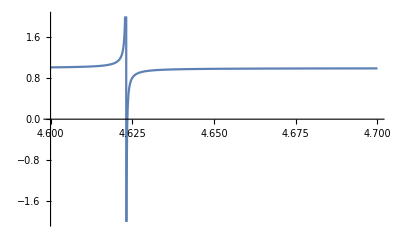

```mathematica
Plot[ascat[10.0,10.0,0.1,.000001,ϵ2],{ϵ2,4.6,4.7},PlotRange->{-2,2}]
```

```mathematica
SolInfo[v1_,v2_,g_,ϵ_,ϵ2_]:=(W=({{(ϵ+v1), g}, {g, (ϵ+v2-ϵ2)}});Avals=Simplify[Eigenvalues[W]];
ϕmat=({{a1 ψIn[L,√Avals[[1]] r]}, {a2 ψIn[L,√Avals[[2]] r]}});AvecsNormed=Transpose[Table[FullSimplify[Normalize[Eigenvectors[W][[n]]]],{n,1,2}]];Solve[{AvecsNormed.ϕmat==({{ψSOut[L,√ϵ r]}, {b2 ψBOut[L,√(ϵ2-ϵ)r]}}),AvecsNormed.D[ϕmat,r]==D[({{ψSOut[L,√ϵ r]}, {b2 ψBOut[L,√(ϵ2-ϵ)r]}}),r]}/.{L->0,r->1},{a1,a2,b2,Kmat}])
```

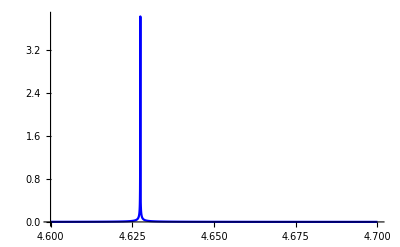

```mathematica
Plot[Abs[a1]/.SolInfo[0.0,10.0,0.1,.000001,ϵ2],{ϵ2,4.6,4.7},PlotStyle->{Black,Red,Blue},PlotRange->All]
```

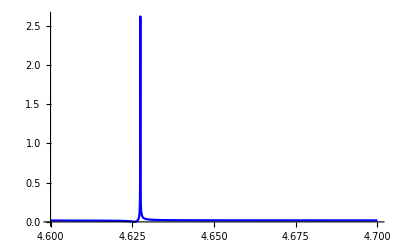

```mathematica
Plot[Abs[a2]/.SolInfo[0.0,10.0,0.1,.000001,ϵ2],{ϵ2,4.6,4.7},PlotStyle->{Black,Red,Blue},PlotRange->All]
```

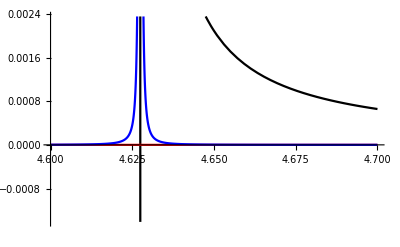

```mathematica
Plot[{Re[a1]/.SolInfo[0.0,10.0,0.1,.000001,ϵ2],
Im[a1]/.SolInfo[0.0,10.0,0.1,.000001,ϵ2],
Abs[a1]^2/.SolInfo[0.0,10.0,0.1,.000001,ϵ2]},{ϵ2,4.6,4.7},PlotStyle->{Black,Red,Blue}]
```

Aha,  the upper channel has an s-wave bound state with binding 4.62419 (with respect to the upper threshold).  Therefore, there should be a zero-energy resonance if the upper threshold is shifted by that binding, consistent with the picture above.  Let’s take a look at the square of the partial wave amplitude |a_l|^2:

```mathematica
aLsqr[v1_,v2_,g_,ϵ_,ϵ2_,L_]:=(
W=({{(ϵ+v1), g}, {g, (ϵ+v2-ϵ2)}});
Avals=Simplify[Eigenvalues[W]];
ϕmat=({{a1 ψIn[L,√Avals[[1]] r]}, {a2 ψIn[L,√Avals[[2]] r]}});AvecsNormed=Transpose[Table[FullSimplify[Normalize[Eigenvectors[W][[n]]]],{n,1,2}]];Abs[Kmat/(1-ⅈ Kmat)]^2/.Solve[{AvecsNormed.ϕmat==({{ψSOut[L,√ϵ r]}, {b2 ψBOut[L,√(ϵ2-ϵ)r]}}),AvecsNormed.D[ϕmat,r]==D[({{ψSOut[L,√ϵ r]}, {b2 ψBOut[L,√(ϵ2-ϵ)r]}}),r]}/.{L->0,r->1},{a1,a2,b2,Kmat}][[1]])
```

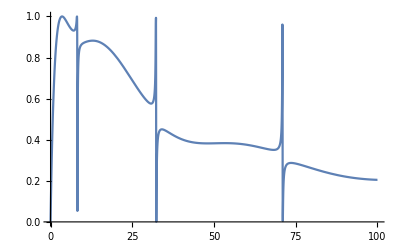

```mathematica
Plot[aLsqr[10.0,100.0,1,ϵ,100,0],{ϵ,0,100},PlotRange->All]
```

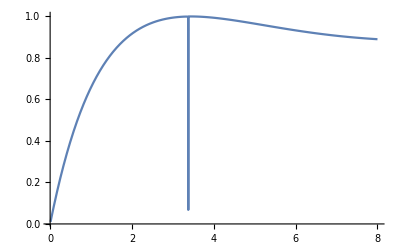

```mathematica
Plot[aLsqr[10.0,10.0,.1,ϵ,8.0,0],{ϵ,0.01,8.0},PlotRange->All,PlotPoints->100]
```

## Generalize to N channels...

Let’s imagine a two-body Hamiltonian in relative coordinates that is of the form:

H=T+V

V=(V_1 | V_12 | V_13 | ⋯
V_21 | V_2 | V_23 | ⋯
V_31 | V_32 | V_3 | ⋯
⋮ | ⋮ | ⋮ | ⋱)

Where Σ is a diagonal matrix with the eigenvalues of W.  We have in region I:

[(∂^2/(∂r^2)-(L(L+1))/r^2 | 0 | 0 | ⋯
0 | ∂^2/(∂r^2)-(L(L+1))/r^2 | 0 | ⋯
0 | 0 | ∂^2/(∂r^2)-(L(L+1))/r^2 | ⋯
⋮ | ⋮ | ⋮ | ⋱)+((ϵ+v_1) | g_12 | ⋯ | g_(1N)
g_12 | (ϵ+v_2-ϵ_2) | ⋯ | g_(2N)
⋮ | ⋮ | ⋱ | ⋮
g_(1N) | g_(2N) | ⋯ | (ϵ+v_N-ϵ_N))](ψ_1^I
 ψ_2^I
⋮
ψ_N^I)=0

Now, we let

W=((ϵ+v_1) | g_12 | ⋯ | g_(1N)
g_12 | (ϵ+v_2-ϵ_2) | ⋯ | g_(2N)
⋮ | ⋮ | ⋱ | ⋮
g_(1N) | g_(2N) | ⋯ | (ϵ+v_N-ϵ_N))

As a simple case, let’s assume that this matrix is tridiagonal, with equal coupling between neighboring channels.  Also assume that all of the potential depths are equal

```mathematica
NCHAN=5;
```

Start with a tridiagonal model:

```mathematica
W=Table[If[i==j,ϵ+v0-ϵ1 i^2,(KroneckerDelta[i,j-1]+ KroneckerDelta[i,j+1])g],{i,1,NCHAN},{j,1,NCHAN}];
```

```mathematica
MatrixForm[W];
```

```mathematica
ϕmat=Table[a[[i]]ψIn[L,√Avals[[i]] r],{i,1,NCHAN}];MatrixForm[ϕmat];
```

```mathematica
SolInfo[v0_,g_,ϵ_,ϵ2_]:=(
W=Table[If[i==j,ϵ+v0-ϵ2 i^2,(KroneckerDelta[i,j-1]+ KroneckerDelta[i,j+1])g],{i,1,NCHAN},{j,1,NCHAN}];

Avals=Simplify[Eigenvalues[W]];
ϕmat=Table[a[[i]]ψIn[L,√Avals[[i]] r],{i,1,NCHAN}];
ψII=Table[If[i==1,ψSOut[L,√ϵ r],b[[i]]ψBOut[L,√(i^2 ϵ2-ϵ)r]],{i,1,NCHAN}];
AvecsNormed=Transpose[Table[FullSimplify[Normalize[Eigenvectors[W][[n]]]],{n,1,2}]];Solve[{AvecsNormed.ϕmat==ψII,AvecsNormed.D[ϕmat,r]==D[ψII,r]}/.{L->0,r->1},{a[[]],b[[]],Kmat}])
```

```mathematica
SolInfo[10,1,.1,.1]
```

Solve[{{{0.570151,-0.591362},{0.67461,-0.0245137},{0.430438,0.582992},{0.179041,0.515074},{0.0499666,0.21097}}.{-0.201156 a⟦1⟧,-0.0272291 a⟦2⟧,0.144502 a⟦3⟧,0.305987 a⟦4⟧,0.511638 a⟦5⟧}=={0.562341 (0.441243+1.34851 Kmat),0.908337 b⟦2⟧,0.642207 b⟦3⟧,0.461551 b⟦4⟧,0.333667 b⟦5⟧},{{0.570151,-0.591362},{0.67461,-0.0245137},{0.430438,0.582992},{0.179041,0.515074},{0.0499666,0.21097}}.{-3.27577 a⟦1⟧,-3.16765 a⟦2⟧,-2.96513 a⟦3⟧,-2.69485 a⟦4⟧,-2.23779 a⟦5⟧}=={0.562341 (0.205814-0.813787 Kmat)+0.281171 (0.441243+1.34851 Kmat),-0.497517 b⟦2⟧,-0.574407 b⟦3⟧,-0.565283 b⟦4⟧,-0.516915 b⟦5⟧}},{a,b,Kmat}]

## scratch work...

```mathematica
Clear[k]
```

```mathematica
ψphys=({{ⅇ^(ⅈ k r)S-ⅇ^(-ⅈ k r)}, {n ⅇ^(-q r)}})
```

{{-ⅇ^(-ⅈ k r)+ⅇ^(ⅈ k r) S},{100 ⅇ^(-1963 r)}}

```mathematica
FullSimplify[D[ψphys,r]]
```

{{ⅈ ⅇ^(-ⅈ k r) k (1+ⅇ^(2 ⅈ k r) S)},{-196300 ⅇ^(-1963 r)}}

```mathematica
SphericalBesselK[L_,z_]:=√(π/(2z))BesselK[L+1/2,z]
```

```mathematica
Simplify[FunctionExpand[x SphericalBesselK[0,x]],Assumptions->{x>0}]
```

(ⅇ^-x π)/2

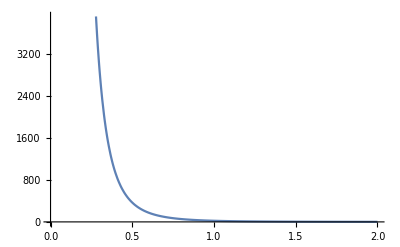

```mathematica
Plot[SphericalBesselK[3,x],{x,0,2}]
```

FunctionExpand::fas: Warning: one or more assumptions evaluated to False.

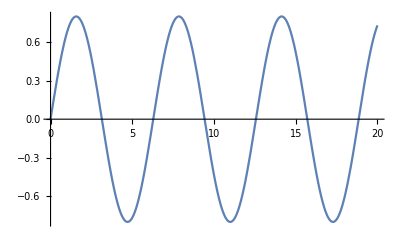

```mathematica
Plot[FullSimplify[FunctionExpand[√x BesselJ[L+1/2,x],Assumptions->{L∈Integers,L>0}]]/.L->1,{x,0,20}]
```

```mathematica
NDEigensystem
```